# Woods-Saxon Potential

## Micah Buuck

6/17/13

## Constants and Initial Conditions

Originally I tried to make use of Mathematica's built-in unit handling, but I couldn't figure out how to make that work with plotting, so I gave up. I left the code for it in, but commented it out.

```mathematica
(*<<Units`
Needs["PhysicalConstants`"]*)
Needs["PlotLegends`"]
```

```mathematica
m=938.272046(*Mega ElectronVolt*);
ℏc=197.32697178(*Mega ElectronVolt*Femto Meter*);
R=3 (*Femto Meter*);
V0=(-1.9-.38*I)*ℏc^2/(2*m) (*Mega ElectronVolt*);
a=.54 (*Femto Meter*);
V[r_]:=V0/(1+E^((r-R)/a));
```

### Plot for potential

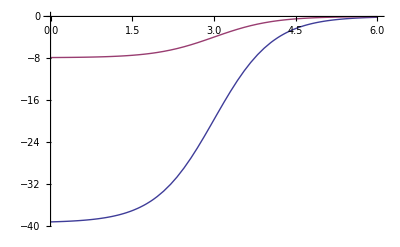

```mathematica
Plot[{Re[V[r]],Im[V[r]]},{r,0,2*R}]
```

## Solve the Schrödinger Equation

First I solve the Schrödinger equation for the radial wavefunction with an arbitrary constant for the initial condition for u'(0). My goal is to show that the resulting phase shift we get from this in independent of the choice of u'(0).

```mathematica
s[L_,k_,b_]:=NDSolve[{u''[r]+(k^2-2*m/(ℏc)^2*V[r]-L*(L+1)/r^2)*u[r]==0,u[(1000*k)^(-1)]==0,u'[(1000*k)^(-1)]==b},u,{r,(1000*k)^(-1),5*R}]
```

```mathematica
u[L_,k_,r_,b_]:=u[r]/.s[L,k,b][[1]]
```

```mathematica
beta[L_,k_,b_]:=5*R/Evaluate[u[L,k,5*R,b]]*(D[u[L,k,r,b],r]/.r->(5*R))-1
tanδ[L_,k_,b_]:=N[(k*5*R*Derivative[0,1][SphericalBesselJ][L,k*5*R]-beta[L,k,b]*SphericalBesselJ[L,k*5*R])/(k*5*R*Derivative[0,1][SphericalBesselY][L,k*5*R]-beta[L,k,b]*SphericalBesselY[L,k*5*R])]
```

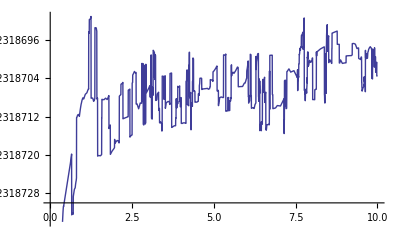

```mathematica
Plot[Re[tanδ[0,1,b]],{b,0.01,10}]
```

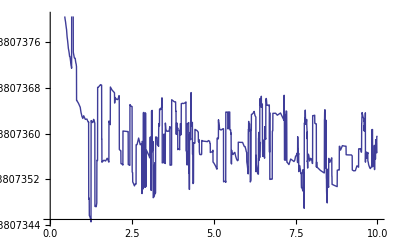

```mathematica
Plot[Im[tanδ[0,1,b]],{b,0.01,10}]
```

As we can see from this plot of tanδ vs. u'(0), the phase shift appears to be independent of our choice of u'(0) up to about 0.01% error.

## Reformulate tanδ for specific choice of u'(0)

These are the same equations as above, but now we have chosen u'(0)=8 (an arbitrary choice).

```mathematica
s[L_,k_]:=NDSolve[{u''[r]+(k^2-2*m/(ℏc)^2*V[r]-L*(L+1)/r^2)*u[r]==0,u[(1000*k)^(-1)]==0,u'[(1000*k)^(-1)]==8},u,{r,(1000*k)^(-1),5*R},MaxSteps->20000]
```

```mathematica
u[L_,k_,r_]:=u[r]/.s[L,k][[1]]
```

```mathematica
beta[L_,k_]:=5*R/Evaluate[u[L,k,5*R]]*(D[u[L,k,r],r]/.r->(5*R))-1
tanδ[L_,k_]:=N[(k*5*R*Derivative[0,1][SphericalBesselJ][L,k*5*R]-beta[L,k]*SphericalBesselJ[L,k*5*R])/(k*5*R*Derivative[0,1][SphericalBesselY][L,k*5*R]-beta[L,k]*SphericalBesselY[L,k*5*R])]
```

```mathematica
Table[tanδ[L,1],{L,0,20}]
```

{-0.923187+0.738074 ⅈ,-1.22237+1.20904 ⅈ,-1.58735+1.99802 ⅈ,1.00564+1.1644 ⅈ,0.211335+0.0713622 ⅈ,0.0403135+0.00963108 ⅈ,0.00812726+0.00172725 ⅈ,0.00165119+0.000337094 ⅈ,0.000333925+0.0000672485 ⅈ,0.0000671337+0.0000134576 ⅈ,0.0000134081+2.6876×10^-6 ⅈ,2.6722×10^-6+5.35051×10^-7 ⅈ,5.30794×10^-7+1.06139×10^-7 ⅈ,1.05238×10^-7+2.09407×10^-8 ⅈ,2.36222×10^-8+4.08615×10^-9 ⅈ,6.62046×10^-9+7.80279×10^-10 ⅈ,1.01519×10^-9+1.43713×10^-10 ⅈ,1.04656×10^-10+2.51393×10^-11 ⅈ,-3.4111×10^-12+4.1209×10^-12 ⅈ,-3.93433×10^-12+6.26806×10^-13 ⅈ,-1.06641×10^-13+8.79197×10^-14 ⅈ}

For k=1, tanδ becomes negligible after about L=5. This is also evident in the plot for continuous L below.

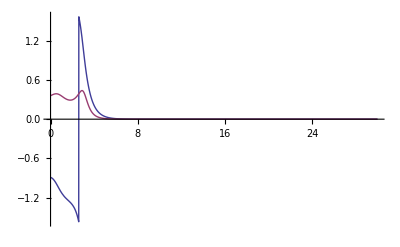

```mathematica
Plot[{Re[ArcTan[tanδ[L,1]]],Im[ArcTan[tanδ[L,1]]]},{L,0,30},PlotRange->{-Pi/2,Pi/2}]
```

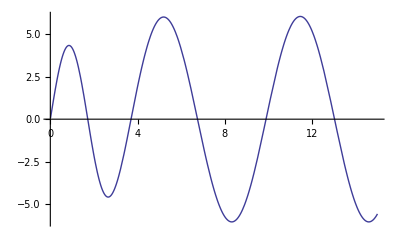

```mathematica
Plot[Evaluate[u[0,1,r]],{r,(100)^(-1),5*R}]
```

Plugging this phase shift into the equations for the scattering amplitude is:

```mathematica
f[k_,θ_]:=1/k*Sum[(2*L+1)*tanδ[L,k]/(1-I*tanδ[L,k])*LegendreP[L,Cos[θ]],{L,0,2*k*R}]
```

Here is a table of some values of dσ/dΩ as a function of θ.

```mathematica
Clear[dσdΩ]
```

```mathematica
dσdΩ[k_]:=Table[{θ,Abs[f[k,θ]]^2},{θ,0,Pi,.1}]
```

```mathematica
dσdΩ[1]
```

{{0.,138.247},{0.1,131.964},{0.2,114.659},{0.3,90.3947},{0.4,64.3083},{0.5,40.965},{0.6,23.1851},{0.7,11.7151},{0.8,5.66352},{0.9,3.31985},{1.,2.93192},{1.1,3.18173},{1.2,3.32365},{1.3,3.09532},{1.4,2.54149},{1.5,1.84548},{1.6,1.20475},{1.7,0.754725},{1.8,0.536269},{1.9,0.502378},{2.,0.554573},{2.1,0.592212},{2.2,0.554527},{2.3,0.440295},{2.4,0.300995},{2.5,0.213979},{2.6,0.247955},{2.7,0.433318},{2.8,0.746707},{2.9,1.11467},{3.,1.43592},{3.1,1.61541}}

```mathematica
interp1=Interpolation[dσdΩ[1]]
```

InterpolatingFunction[{{0.,3.1}},<>]

Here is a log plot of that same information.

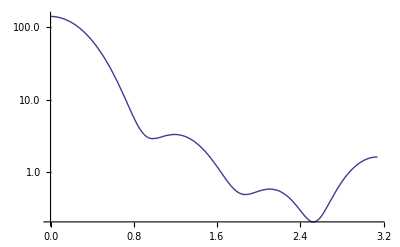

```mathematica
p1=LogPlot[interp1[θ],{θ,0,Pi}]
```

## Eikonal Approximation

These equations come straight out of Sakurai, equations 7.4.13 and 7.4.14 (page 394).

```mathematica
χ0[k_,b_?NumericQ]:=-2*m/(k*(ℏc)^2)*NIntegrate[V[Sqrt[b^2+z^2]],{z,0,15}]
T0[k_,b_?NumericQ]:=Exp[I*χ0[k,b]]-1
Eif0[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T0[k,b],{b,0,15}]
```

I had to have the iteration of the table below happen in integer steps because doing it in decimal steps was giving Mathematica problems somehow. I think it probably has something to do with differences in the way it handles integers and floats.

```mathematica
Abs[Eif0[1,1]]^2
```

2.75535

```mathematica
eik0dσdΩ[k_]:=Table[{θ/10.,Abs[Eif0[k,θ/10]]^2},{θ,0,10*Pi,1}]
```

```mathematica
eik0dσdΩ[1]
```

{{0,77.8145},{0.1,74.3538},{0.2,64.8484},{0.3,51.5799},{0.4,37.3777},{0.5,24.6842},{0.6,14.949},{0.7,8.51792},{0.8,4.91523},{0.9,3.28187},{1.,2.75535},{1.1,2.68571},{1.2,2.69029},{1.3,2.60681},{1.4,2.41047},{1.5,2.13884},{1.6,1.84253},{1.7,1.56116},{1.8,1.31704},{1.9,1.11769},{2.,0.961143},{2.1,0.840945},{2.2,0.749472},{2.3,0.679774},{2.4,0.626292},{2.5,0.584923},{2.6,0.552808},{2.7,0.528029},{2.8,0.50934},{2.9,0.495947},{3.,0.487366},{3.1,0.483321}}

```mathematica
eik0interp1=Interpolation[%]
```

InterpolatingFunction[{{0.,3.1}},<>]

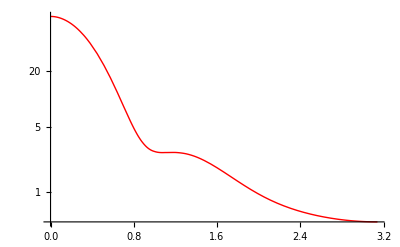

```mathematica
eik0p1=LogPlot[eik0interp1[θ],{θ,0,Pi},PlotStyle->Red]
```

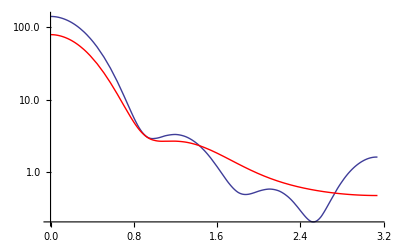

```mathematica
Show[p1,eik0p1]
```

As you can see above, the two plots actually agree with each other pretty well, especially at small θ. There is some pretty obvious disagreement for large θ, however, and the eikonal approximation seems to miss some of the structure apparent in the partial wave formulation.

## Check Method for k=10

For k=10, then k^2 = 100 >> 2*m*V/ℏ^2 ~= -2 - 0.4i, so the eikonal approximation should be valid.

```mathematica
dσdΩ[10]//Timing
```

{510.822,{{0.,486.366},{0.1,13.7655},{0.2,0.142722},{0.3,0.00212583},{0.4,0.000122783},{0.5,1.06992×10^-6},{0.6,3.82125×10^-6},{0.7,1.5606×10^-6},{0.8,9.09828×10^-7},{0.9,4.56746×10^-7},{1.,2.06863×10^-7},{1.1,7.29154×10^-8},{1.2,1.35146×10^-8},{1.3,1.44845×10^-9},{1.4,1.86539×10^-8},{1.5,5.22517×10^-8},{1.6,9.36151×10^-8},{1.7,1.35377×10^-7},{1.8,1.73879×10^-7},{1.9,2.03822×10^-7},{2.,2.24481×10^-7},{2.1,2.3388×10^-7},{2.2,2.31779×10^-7},{2.3,2.17965×10^-7},{2.4,1.94183×10^-7},{2.5,1.61737×10^-7},{2.6,1.23014×10^-7},{2.7,8.11484×10^-8},{2.8,4.02909×10^-8},{2.9,8.73381×10^-9},{3.,6.19344×10^-9},{3.1,1.49821×10^-7}}}

The first number above is the time that command took to evaluate.

```mathematica
interp10=Interpolation[%[[2]]];
```

InterpolatingFunction[{{0.,3.1}},<>]

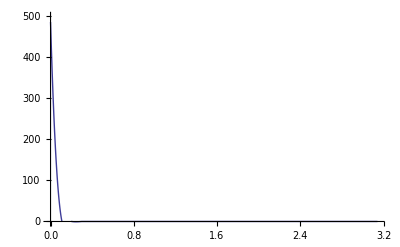

```mathematica
p10=Plot[interp10[θ],{θ,0,Pi},PlotRange->{-1,500}]
```

```mathematica
eik0dσdΩ[10]//Timing
```

{225.703,{{0,486.162},{0.1,14.0605},{0.2,0.13689},{0.3,0.00246745},{0.4,0.0000540022},{0.5,1.42675×10^-6},{0.6,3.23853×10^-8},{0.7,1.29725×10^-9},{0.8,5.91253×10^-11},{0.9,1.26869×10^-11},{1.,8.34575×10^-12},{1.1,3.54278×10^-12},{1.2,2.08122×10^-12},{1.3,1.19259×10^-12},{1.4,7.31612×10^-13},{1.5,4.70504×10^-13},{1.6,3.14678×10^-13},{1.7,2.18652×10^-13},{1.8,1.57428×10^-13},{1.9,1.16839×10^-13},{2.,8.94036×10^-14},{2.1,7.03232×10^-14},{2.2,5.67563×10^-14},{2.3,4.69704×10^-14},{2.4,3.98201×10^-14},{2.5,3.45317×10^-14},{2.6,3.05815×10^-14},{2.7,2.77058×10^-14},{2.8,2.55993×10^-14},{2.9,2.41731×10^-14},{3.,2.32565×10^-14},{3.1,2.28285×10^-14}}}

You can see that as k increases, the eikonal approximation evaluates faster than the partial wave expansion, as we would expect.

```mathematica
eik0interp10=Interpolation[%[[2]]];
```

InterpolatingFunction[{{0.,3.1}},<>]

The points we evaluated dσ/dΩ at are not dense enough to really capture all the detail at small θ, so that's why the plots for k = 10 aren't very good. A better interpolation could be made, but it would take some time.

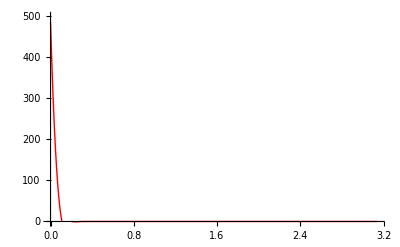

```mathematica
eik0p10=Plot[eik0interp10[θ],{θ,0,Pi},PlotRange->{-1,500},PlotStyle->Red]
```

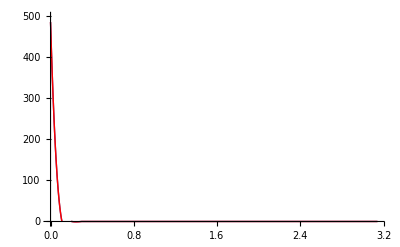

```mathematica
Show[p10,eik0p10]
```

## Plots for k=1,2,3

```mathematica
interp2=Interpolation[dσdΩ[2]];
eik0interp2=Interpolation[eik0dσdΩ[2]];
```

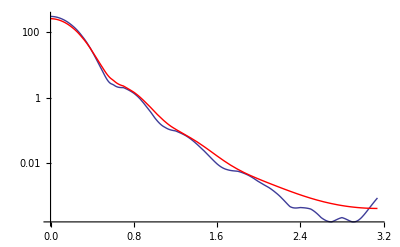

```mathematica
p2=LogPlot[interp2[θ],{θ,0,Pi}];
eik0p2=LogPlot[eik0interp2[θ],{θ,0,Pi},PlotStyle->Red];
Show[p2,eik0p2]
```

```mathematica
interp3=Interpolation[dσdΩ[3]];
eik0interp3=Interpolation[eik0dσdΩ[3]];
```

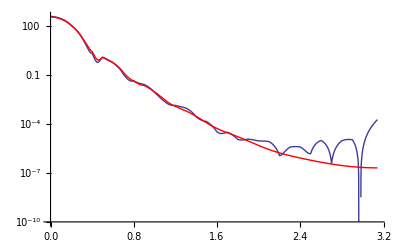

```mathematica
p3=LogPlot[interp3[θ],{θ,0,Pi}];
eik0p3=LogPlot[eik0interp3[θ],{θ,0,Pi},PlotStyle->Red];
Show[p3,eik0p3]
```

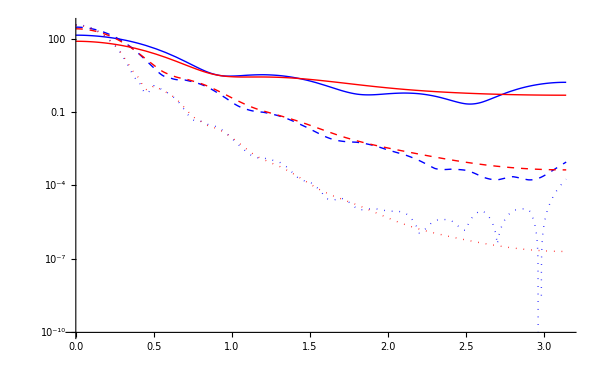

```mathematica
LogPlot[{interp1[θ],eik0interp1[θ],interp2[θ],eik0interp2[θ],interp3[θ],eik0interp3[θ]},{θ,0,Pi},PlotStyle->{{Blue},{Red},{Blue,Dashed},{Red,Dashed},{Blue,Dotted},{Red,Dotted}},PlotLegend->{"Partial Wave: k=1","Eikonal: k=1","Partial Wave: k=2","Eikonal: k=2","Partial Wave: k=3","Eikonal: k=3"},LegendPosition->{1.1,-0.4},LegendSize->{1,1},ImageSize->600]
```

The eikonal approximation actually appears to track the partial wave expansion quite well for k = 1, 2, and 3, but is again missing a lot of the finer structure.

## Plot for k=0.1

As you can see below, the approximation gets pretty bad as k -> 0.

```mathematica
Abs[f[.1,0]]^2
```

9.73572

```mathematica
Abs[Eif0[.1,0]]^2
```

2.19448

```mathematica
interp01=Interpolation[dσdΩ[.1]];
eik0interp01=Interpolation[eik0dσdΩ[.1]];
```

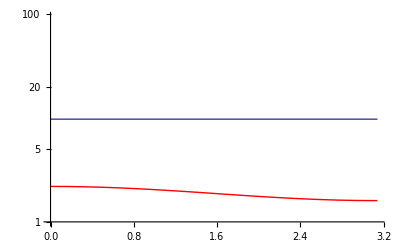

```mathematica
p01=LogPlot[interp01[θ],{θ,0,Pi}];
eik0p01=LogPlot[eik0interp01[θ],{θ,0,Pi},PlotStyle->Red];
Show[p01,eik0p01]
```

## Add in Eikonal Corrections

### First order correction

```mathematica
En[k_]:=(k*ℏc)^2/(2*m)
U[r_]:=V[r]/V0
ϵ[k_]:=V0/(2*En[k])
```

```mathematica
(2#+b^1*D[#,{b,1}])&[Sin[b]]
```

b Cos[b]+2 Sin[b]

```mathematica
τ1[k_,b_]=-k*ϵ[k]^2*NIntegrate[Evaluate[(1#+b*D[#,{b,1}])&[U[Sqrt[z^2+b^2]]^2]],{z,0,15}];
```

```mathematica
T1[k_,b_]:=Exp[I(χ0[k,b]+τ1[k,b])]-1
Eif1[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T1[k,b],{b,0,15}]
```

```mathematica
eik1dσdΩ[k_]:=Table[{θ/10.,Abs[Eif1[k,θ/10]]^2},{θ,0,10*Pi,1}]
```

```mathematica
eik1dσdΩ[1]
```

```mathematica
eik1interp1=Interpolation[%];
```

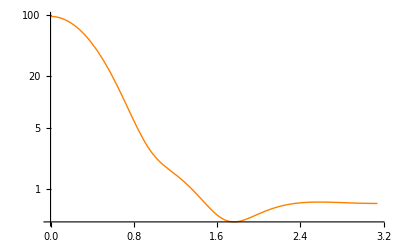

```mathematica
eik1p1=LogPlot[eik1interp1[θ],{θ,0,Pi},PlotStyle->Orange]
```

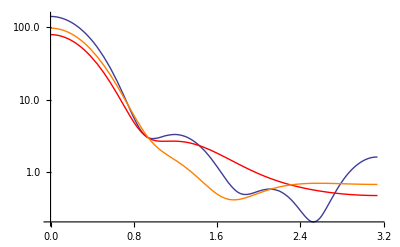

```mathematica
Show[p1,eikp1,eik1p1]
```

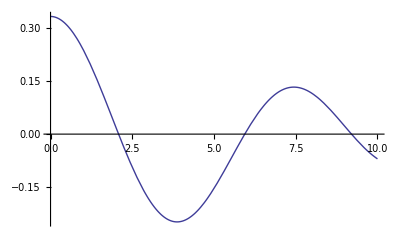

```mathematica
Plot[{Operate[Derivative[0,1],SphericalBesselJ[1,x]]/.x->y},{y,0,10}]
```

```mathematica
g=Identity+Derivative[0,1];
```

```mathematica
Plot[Operate[g,SphericalBesselJ[1,y]]/.y->x,{x,0,10}]
```

-Graphics-

```mathematica
{Derivative[1][h],Derivative[3][h][x],Derivative[2][h]}
Sin[x]
```

{h',h^(3)[x],h''}

Sin[x]